```mathematica
b=2
d=1
```

2

1

```mathematica
//Slide this to change g parameter
```

```mathematica
Clear[g]
```

```mathematica
g=1
```

1

```mathematica
N[Eigenvalues[{{2*d-g,-g,-g},{-g,4*d-g,-g},{-g,-g,6*d-g}}]]
```

{5.48929,3.28917,0.221543}

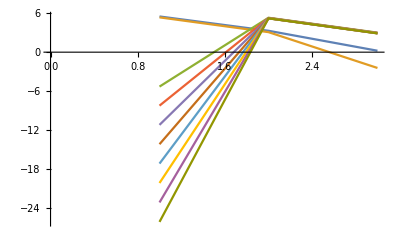

```mathematica
ListLinePlot[Table[Eigenvalues[{{2*d-g,-g,-g},{-g,4*d-g,-g},{-g,-g,6*d-g}}],{g,10}]]
```

```mathematica
A bit confusing of a graph. Unfortunately it was the only way I could figure to plot the eigenvalues as a function of the interaction term g. The eigen values themselves are on the x axis. Eigenvalue one is at x=1, eigen value 2 is at x=2,and so on. We see as g is increased to 10 eigen value 1 increases negatively. While eigenvalues 2 and 3 converge to the same number. 
Below I give the eigen vectors and values for g=10 b=2, d=1.

Clear[g]
```

```mathematica
g=10
```

10

```mathematica
N[Eigenvalues[{{2*d-g,-g,-g},{-g,4*d-g,-g},{-g,-g,6*d-g}}]]//MatrixForm
```

(-26.0888
5.19823
2.89053)

```mathematica
N[Eigenvectors[{{2*d-g,-g,-g},{-g,4*d-g,-g},{-g,-g,6*d-g}}]]//MatrixForm
```

(1.14241 | 1.06647 | 1.
-0.250692 | -0.669131 | 1.
-3.49171 | 2.80266 | 1.)